## G(T) for p0=3.825

```mathematica
(*saveFolder="/Users/chengling/Learning/Research/TempDirForRemote/p380TauAlpha/N4096/";*)
```

```mathematica
saveFolder="/home/chengling/Research/Project/Cell/glassyDynamics/N4096/p385/";
```

```mathematica
Directory[]
```

/home/chengling

```mathematica
Tlist={0.063, 0.039 ,0.03105 ,0.025, 0.016 ,0.01, 0.008 ,0.0063, 0.005 ,0.00385 ,0.0031 ,0.0028 ,0.0025 ,0.0022 ,0.002 ,0.0018, 0.001, 0.00067 ,0.0005 ,0.0004, 0.00033,0.00025 ,0.00018,0.00014,0.0001};
```

```mathematica
Tstring=ToString[NumberForm[#,{9,8},ExponentFunction->(Null&)]]&/@Tlist
```

{0.06300000,0.03900000,0.03105000,0.02500000,0.01600000,0.01000000,0.00800000,0.00630000,0.00500000,0.00385000,0.00310000,0.00280000,0.00250000,0.00220000,0.00200000,0.00180000,0.00100000,0.00067000,0.00050000,0.00040000,0.00033000,0.00025000,0.00018000,0.00014000,0.00010000}

```mathematica
Length[Tlist]
```

25

```mathematica
spacing={22,22,22,22,22,26,30,221,243,313,400,400,400,400,400,400,400,400,400,400,400,400,400,400,400};
```

```mathematica
Length[spacing]
```

25

```mathematica
derivatives=Table[Table[Import[StringJoin[saveFolder,"SigmaSecD_N4096_p3.8500_T",Tstring[[T]],"_Spacing",ToString[spacing[[T]]],"_idx",ToString[i],".nc"],"Data"],{i,0,2}],{T,Length[Tlist]}];
```

```mathematica
g1=Table[Mean[Table[Mean[Normal[derivatives[[T,i,2]]][[Floor[Length[derivatives[[T,i,2]]]/2];;]]]/4096,{i,3}]],{T,Length[Tlist]}]
```

{0.641734,0.521614,0.47248,0.430947,0.359126,0.302429,0.281656,0.26265,0.247516,0.233651,0.224371,0.22064,0.216809,0.212954,0.210314,0.207724,0.196889,0.191916,0.18914,0.187391,0.186001,0.184299,0.182739,0.18153,0.180218}

```mathematica
g2=Table[Mean[Table[Variance[Normal[derivatives[[T,i,1]]*4096][[Floor[Length[derivatives[[T,i,2]]]/2];;]]],{i,3}]]/4096/Tlist[[T]],{T,Length[Tlist]}]
```

{0.447222,0.389704,0.365551,0.343733,0.304173,0.263368,0.249,0.242846,0.226967,0.220263,0.21245,0.211668,0.206463,0.204593,0.20365,0.200536,0.192334,0.191096,0.187518,0.185015,0.184522,0.183229,0.181496,0.181417,0.179591}

```mathematica
g1s=Table[Table[Mean[Normal[derivatives[[T,i,2]]][[Floor[Length[derivatives[[T,i,2]]]/2];;]]]/4096,{i,3}],{T,Length[Tlist]}]
```

{{0.641734,0.641519,0.641948},{0.521575,0.521605,0.521663},{0.472535,0.47245,0.472454},{0.430917,0.431,0.430923},{0.359204,0.359232,0.358943},{0.302379,0.302497,0.302411},{0.281757,0.281662,0.281548},{0.262743,0.262608,0.2626},{0.247572,0.247524,0.247451},{0.233608,0.233684,0.233661},{0.22436,0.224355,0.224397},{0.220616,0.220654,0.220651},{0.216797,0.216839,0.216792},{0.212891,0.212975,0.212997},{0.21031,0.210303,0.210328},{0.207773,0.207707,0.207693},{0.196976,0.196856,0.196836},{0.191901,0.191964,0.191884},{0.189154,0.189113,0.189154},{0.187385,0.187495,0.187294},{0.18578,0.186119,0.186104},{0.184378,0.184126,0.184394},{0.182875,0.182646,0.182696},{0.181474,0.181641,0.181476},{0.179843,0.180376,0.180436}}

```mathematica
g2s=Table[Table[Variance[Normal[derivatives[[T,i,1]]*4096][[Floor[Length[derivatives[[T,i,2]]]/2];;]]],{i,3}]/4096/Tlist[[T]],{T,Length[Tlist]}]
```

{{0.443685,0.449757,0.448223},{0.398185,0.388864,0.382064},{0.363165,0.369827,0.36366},{0.341561,0.347058,0.34258},{0.299951,0.30991,0.302657},{0.26056,0.263701,0.265843},{0.250015,0.249618,0.247366},{0.243725,0.238904,0.245909},{0.22651,0.227313,0.227076},{0.222853,0.21604,0.221895},{0.211042,0.213151,0.213157},{0.211307,0.2113,0.212399},{0.209761,0.205266,0.204361},{0.203562,0.203703,0.206515},{0.204163,0.203733,0.203055},{0.199732,0.200059,0.201818},{0.194355,0.192671,0.189977},{0.190948,0.189308,0.193033},{0.186911,0.188296,0.187348},{0.185834,0.184685,0.184526},{0.184674,0.183449,0.185441},{0.183637,0.184566,0.181483},{0.181739,0.179562,0.183187},{0.179996,0.182374,0.181881},{0.178447,0.179776,0.180551}}

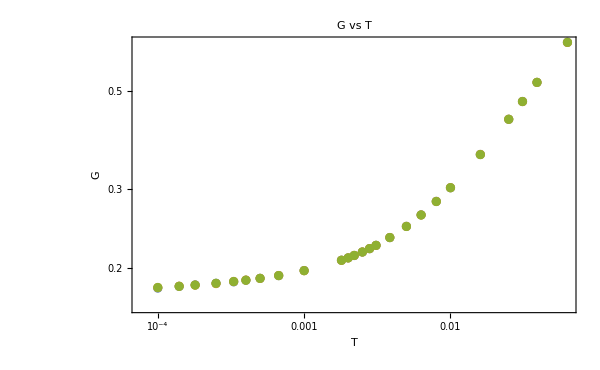

```mathematica
ListLogLogPlot[Table[Table[{Tlist[[T]],g1s[[T,i]]},{T,Length[Tlist]}],{i,3}],FrameLabel->{"T","G"},ImageSize->600,PlotLabel->"G vs T"]
```

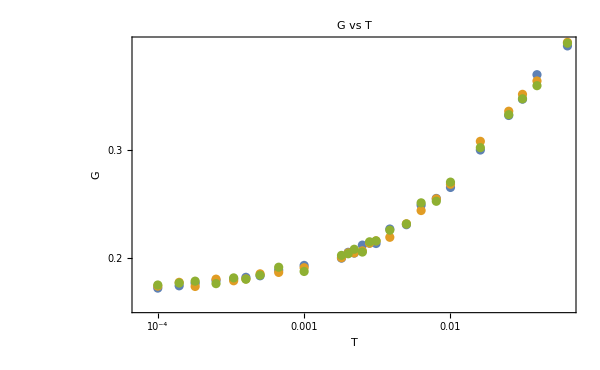

```mathematica
ListLogLogPlot[Table[Table[{Tlist[[T]],g2s[[T,i]]},{T,Length[Tlist]}],{i,3}],FrameLabel->{"T","G"},ImageSize->600,PlotLabel->"G vs T"]
```

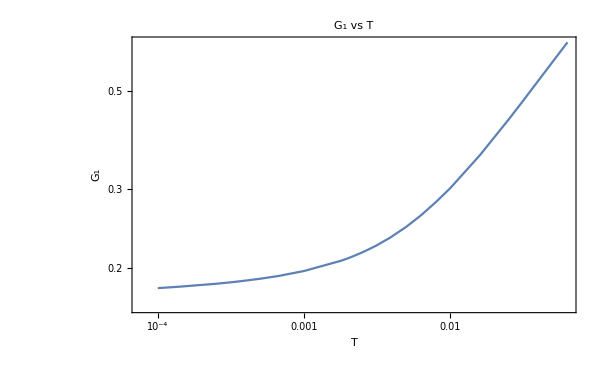

```mathematica
G1Plot=ListLogLogPlot[Table[{Tlist[[T]],g1[[T]]},{T,Length[Tlist]}],FrameLabel->{"T","G_1"},ImageSize->600,PlotLabel->"G_1 vs T",Joined->True]
```

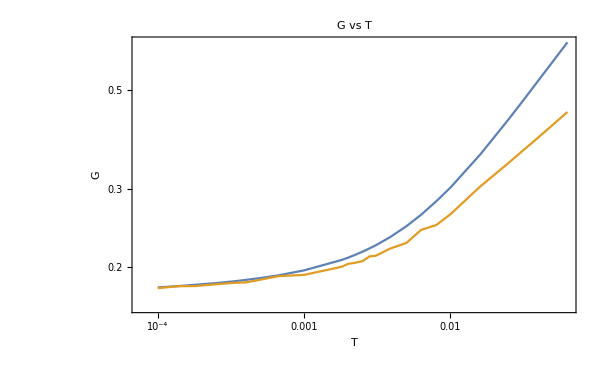

```mathematica
G2Plot=ListLogLogPlot[{Table[{Tlist[[T]],g1[[T]]},{T,Length[Tlist]}],Table[{Tlist[[T]],g2[[T]]},{T,Length[Tlist]}]},FrameLabel->{"T","G"},ImageSize->600,PlotLabel->"G vs T",Joined->True,PlotLabel->{"G_1,G_2"}]
```

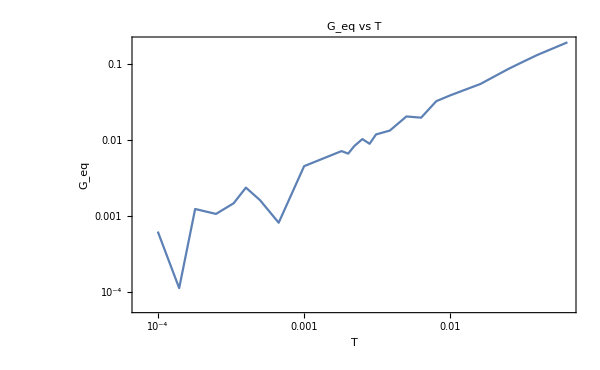

```mathematica
GeqPlot=ListLogLogPlot[Table[{Tlist[[T]],g1[[T]]-g2[[T]]},{T,Length[Tlist]}],FrameLabel->{"T","G_eq"},ImageSize->600,PlotLabel->"G_eq vs T",Joined->True]
```

### fitting

```mathematica
GT[A_,T_,B_]:=A T^B;
```

```mathematica
g1fitting1=NonlinearModelFit[Table[{Tlist[[T]],g1[[T]]},{T,Floor[Length[Tlist]/3]}],{GT[A,t,B]},{A,B},t]
```

FittedModel[1.919 t^0.400659]

```mathematica
g1fitting2=NonlinearModelFit[Table[{Tlist[[T]],g1[[T]]},{T,Length[Tlist]-3,Length[Tlist]}],{GT[A,t,B]},{A,B},t]
```

FittedModel[0.225918 t^0.0245844]

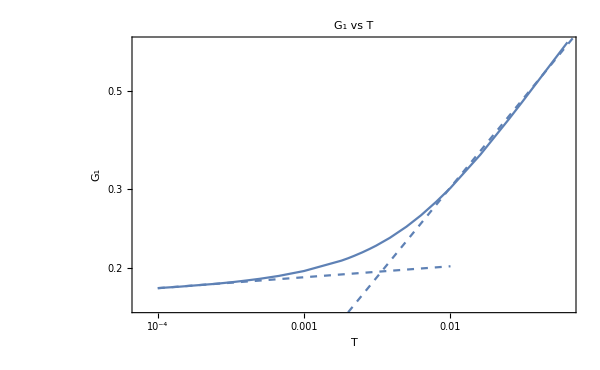

```mathematica
Show[G1Plot,LogLogPlot[g1fitting1[x],{x,0.001,0.1},PlotStyle->Dashed],LogLogPlot[g1fitting2[x],{x,0.0001,0.01},PlotStyle->Dashed]]
```

```mathematica
geqfitting=NonlinearModelFit[Table[{Tlist[[T]],g1[[T]]-g2[[T]]},{T,Length[Tlist]}],{GT[A,t,B]},{A,B},t]
```

FittedModel[2.4281 t^0.906767]

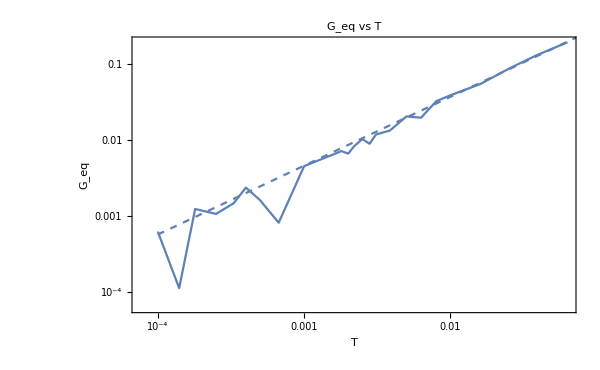

```mathematica
Show[GeqPlot,LogLogPlot[geqfitting[x],{x,0.0001,0.1},PlotStyle->Dashed,PlotLegends->Automatic]]
```

```mathematica
Table[{Tlist[[T]],g1[[T]]},{T,Length[Tlist]}]
```

{{0.063,0.641734},{0.039,0.521614},{0.03105,0.47248},{0.025,0.430947},{0.016,0.359126},{0.01,0.302429},{0.008,0.281656},{0.0063,0.26265},{0.005,0.247516},{0.00385,0.233651},{0.0031,0.224371},{0.0028,0.22064},{0.0025,0.216809},{0.0022,0.212954},{0.002,0.210314},{0.0018,0.207724},{0.001,0.196889},{0.00067,0.191916},{0.0005,0.18914},{0.0004,0.187391},{0.00033,0.186001},{0.00025,0.184299},{0.00018,0.182739},{0.00014,0.18153},{0.0001,0.180218}}

```mathematica
Table[{Tlist[[T]],g1[[T]]-g2[[T]]},{T,Length[Tlist]}]
```

{{0.063,0.194512},{0.039,0.13191},{0.03105,0.106929},{0.025,0.0872136},{0.016,0.0549537},{0.01,0.0390609},{0.008,0.0326562},{0.0063,0.0198042},{0.005,0.0205488},{0.00385,0.0133885},{0.0031,0.0119209},{0.0028,0.00897207},{0.0025,0.0103468},{0.0022,0.00836099},{0.002,0.00666361},{0.0018,0.00718785},{0.001,0.00455524},{0.00067,0.000819716},{0.0005,0.00162187},{0.0004,0.00237666},{0.00033,0.00147935},{0.00025,0.00107051},{0.00018,0.00124317},{0.00014,0.00011296},{0.0001,0.000627022}}

### G(t)=SACF*β*Area+Geq

```mathematica
data=Import["/home/chengling/Research/Project/Cell/glassyDynamics/N4096/SACtime_N4096_p3.8000_T0.00337100_waitingTime5times464.15_idx2.nc","Data"]
```

<|/firstValue→NumericArray[…],/secondValue→NumericArray[…]|>

```mathematica
data[[2,130]]
```

2949.12

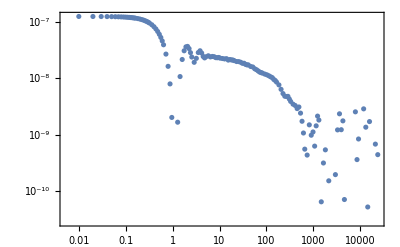

```mathematica
ListLogLogPlot[Table[{data[[2,t]],data[[1,t]]},{t,Length[data[[1]]]}],PlotRange->All]
```